```mathematica
(*Calibrated data from 25 portfolios*)
(*Normalizing factor*)
nf = 12; (* =12 if monthly data, =52 if yearly data *)
dataset = Import["/Users/xiaofeis/Documents/25Portfolios_C2.csv","CSV"];
n=100;
M=200;
NT=500000;
T = 50000;
dT = 0.1;
f[x_]:=Exp[-r*(x-1)*dT];
Disc=Array[f,NT+1];
Nport = 25;
μ=ConstantArray[0,Nport];
σ=ConstantArray[0,Nport];
θ=ConstantArray[0,Nport];
x0=ConstantArray[0,Nport];
LMW=ConstantArray[0,Nport];
CL=ConstantArray[0,Nport];
LR=ConstantArray[0,{Nport,n+1}];
γ=1.5*nf;
σX=1/nf;
r=0.037/nf;
aD=0.05/nf;
σD=0.2853/√nf;
γ=1.5*nf;
σX=1/nf;
r=0.037/nf;
aD=0.05/nf;
σD=0.2853/√nf;
θbar=5;
Pbar=aD/r-θbar*γ*σD^2;
V̄ = (1/nf)^2;
DiffConst=ConstantArray[0,M];
DiffStoch=ConstantArray[0,{M,n+1}];
(*Simulated results*)
For[i=1,i<Nport+1,i++,ILLQ = dataset[[All,i+1]][[2;;]];
par=FindProcessParameters[0.01*Pbar*ILLQ,CoxIngersollRossProcess[a,b,c,d],ProcessEstimator->"MaximumLikelihood"];
μ[[i]]=a/.par[[1]];
σ[[i]]=b/.par[[2]];
θ[[i]]=c/.par[[3]];
x0[[i]]=d/.par[[4]];
κ       = θ[[i]];
λbar=Mean[ILLQ]*0.01*Pbar;
λ=λbar/σX^2 ;
X̄=μ[[i]];
l = (X̄)/(V̄);
(*Illiquidity discount in the LMW model*)
LMW[[i]] =- (θbar*γ^2*σD^2*((2*r*γ)/3*σX^4/σD^2)^(1/3)*λbar^(2/3))/Pbar;
η       = σ[[i]]/√l;
V0     = x0[[i]]/l;
CCtilde=(2*γ^2*θbar*((2*r*γ*σD^4)/3)^(1/3)*√(r+κ))/(√(r+κ+2*r*γ^2*η*θbar*σD)+√(r+κ-2*r*γ^2*η*θbar*σD));
CC=(2 √(r+κ)-√(r+κ+2*r*γ^2*η*θbar*σD)-√(r+κ-2*r*γ^2*η*θbar*σD))/(2*η)*√(r+κ);
κtilde=κ-CC*η;

(*Simulation*)
Vt = V̄*κ/κtilde;
Print[Vt];
For[m=1,m<M+1,m++,Vtilde=RandomFunction[CoxIngersollRossProcess[Vt,η,κtilde,V0],{0,T,dT}];
Vprime=RandomFunction[CoxIngersollRossProcess[V̄,η,κ,V0],{0,T,dT}];
DiffConst[[m]]=-r*CCtilde*λbar^(2/3)*Total[Vtilde["Values"]^(2/3)*Disc*dT];
For[k=1, k<n+2, k++,
ρ=(k-1)/n;
DiffStoch[[m,k]]=-r*CCtilde*λ^(2/3)*Total[Vtilde["Values"]^(2/3)*(ρ*Vtilde["Values"]+(1-ρ)*Vprime["Values"])^(2/3)*Disc*dT];];
];
(*Constant liquidity*)
CL[[i]]=Mean[DiffConst]/Pbar;
(*Liquidity risk*)
LR[[i]]=Mean[DiffStoch]/Pbar;
]
```

0.00699399

0.00696572

0.00696024

0.00695497

0.00695573

0.0069536

0.00695399

0.00695237

0.00695374

0.00695103

0.00695045

0.00695043

0.00694928

0.00694704

0.0069487

0.00694762

0.00694713

0.00694564

0.00694563

0.00694525

0.0069448

0.00694477

0.0069446

0.00694451

0.00694445

```mathematica
LRlow = ConstantArray[0,Nport];
LRup = ConstantArray[0,Nport];
For[i=1,i<Nport+1,i++,
LRlow[[i]] = LR[[i,1]];
LRup[[i]] = LR[[i,100]];
];
```

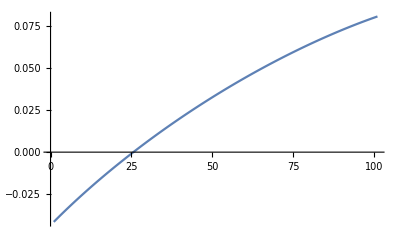

```mathematica
ListLinePlot[LR[[1]]/CL[[1]]-1,PlotRange->All]
```

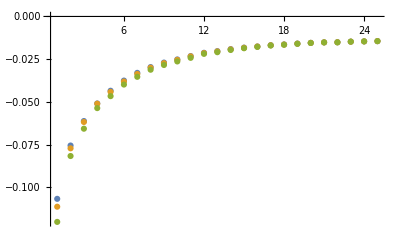

```mathematica
ListPlot[{LRlow,CL,LRup},PlotRange->All]
```

```mathematica
LR
```

{{-0.106732,-0.106946,-0.107157,-0.107366,-0.107571,-0.107774,-0.107975,-0.108173,-0.108369,-0.108563,-0.108755,-0.108944,-0.109132,-0.109317,-0.109501,-0.109683,-0.109863,-0.110041,-0.110217,-0.110392,-0.110565,-0.110737,-0.110906,-0.111075,-0.111241,-0.111407,-0.11157,-0.111733,-0.111893,-0.112053,-0.112211,-0.112367,-0.112522,-0.112676,-0.112828,-0.11298,-0.113129,-0.113278,-0.113425,-0.113571,-0.113716,-0.113859,-0.114001,-0.114142,-0.114282,-0.114421,-0.114558,-0.114694,-0.114829,-0.114963,-0.115096,-0.115227,-0.115357,-0.115487,-0.115615,-0.115742,-0.115868,-0.115992,-0.116116,-0.116238,-0.11636,-0.11648,-0.116599,-0.116717,-0.116834,-0.11695,-0.117065,-0.117178,-0.117291,-0.117403,-0.117513,-0.117622,-0.117731,-0.117838,-0.117944,-0.118049,-0.118153,-0.118255,-0.118357,-0.118457,-0.118557,-0.118655,-0.118752,-0.118848,-0.118943,-0.119037,-0.11913,-0.119221,-0.119311,-0.119401,-0.119488,-0.119575,-0.119661,-0.119745,-0.119828,-0.11991,-0.11999,-0.120069,-0.120147,-0.120223,-0.120298},{-0.0755292,-0.0756271,-0.075724,-0.0758197,-0.0759144,-0.076008,-0.0761007,-0.0761923,-0.0762831,-0.0763728,-0.0764617,-0.0765497,-0.0766368,-0.076723,-0.0768084,-0.076893,-0.0769767,-0.0770597,-0.0771418,-0.0772232,-0.0773038,-0.0773836,-0.0774627,-0.077541,-0.0776187,-0.0776955,-0.0777717,-0.0778472,-0.077922,-0.0779961,-0.0780695,-0.0781422,-0.0782142,-0.0782856,-0.0783564,-0.0784265,-0.0784959,-0.0785647,-0.0786328,-0.0787003,-0.0787672,-0.0788335,-0.0788992,-0.0789642,-0.0790286,-0.0790924,-0.0791556,-0.0792182,-0.0792802,-0.0793416,-0.0794024,-0.0794627,-0.0795223,-0.0795813,-0.0796398,-0.0796977,-0.079755,-0.0798117,-0.0798678,-0.0799234,-0.0799784,-0.0800328,-0.0800866,-0.0801399,-0.0801926,-0.0802447,-0.0802962,-0.0803472,-0.0803976,-0.0804474,-0.0804967,-0.0805454,-0.0805935,-0.080641,-0.080688,-0.0807343,-0.0807801,-0.0808254,-0.08087,-0.0809141,-0.0809575,-0.0810004,-0.0810427,-0.0810844,-0.0811255,-0.081166,-0.0812059,-0.0812451,-0.0812838,-0.0813219,-0.0813593,-0.0813961,-0.0814323,-0.0814678,-0.0815027,-0.0815369,-0.0815705,-0.0816034,-0.0816356,-0.0816671,-0.081698},{-0.0612007,-0.061272,-0.0613426,-0.0614124,-0.0614814,-0.0615498,-0.0616174,-0.0616843,-0.0617506,-0.0618161,-0.0618811,-0.0619453,-0.062009,-0.062072,-0.0621345,-0.0621963,-0.0622576,-0.0623182,-0.0623783,-0.0624378,-0.0624968,-0.0625552,-0.0626131,-0.0626704,-0.0627273,-0.0627835,-0.0628393,-0.0628946,-0.0629493,-0.0630036,-0.0630573,-0.0631106,-0.0631633,-0.0632156,-0.0632674,-0.0633187,-0.0633696,-0.0634199,-0.0634699,-0.0635193,-0.0635683,-0.0636168,-0.0636649,-0.0637125,-0.0637597,-0.0638064,-0.0638527,-0.0638985,-0.0639439,-0.0639889,-0.0640334,-0.0640774,-0.0641211,-0.0641643,-0.0642071,-0.0642494,-0.0642914,-0.0643329,-0.0643739,-0.0644146,-0.0644548,-0.0644946,-0.0645339,-0.0645729,-0.0646114,-0.0646495,-0.0646872,-0.0647244,-0.0647612,-0.0647976,-0.0648336,-0.0648692,-0.0649043,-0.064939,-0.0649732,-0.0650071,-0.0650405,-0.0650735,-0.065106,-0.0651382,-0.0651699,-0.0652011,-0.0652319,-0.0652623,-0.0652922,-0.0653217,-0.0653507,-0.0653793,-0.0654075,-0.0654351,-0.0654623,-0.0654891,-0.0655154,-0.0655412,-0.0655665,-0.0655914,-0.0656157,-0.0656396,-0.065663,-0.0656858,-0.0657082},{-0.0509251,-0.0509703,-0.051015,-0.0510591,-0.0511028,-0.051146,-0.0511888,-0.0512311,-0.0512729,-0.0513143,-0.0513553,-0.0513958,-0.0514359,-0.0514756,-0.0515149,-0.0515538,-0.0515923,-0.0516304,-0.0516681,-0.0517054,-0.0517424,-0.0517789,-0.0518151,-0.0518509,-0.0518864,-0.0519215,-0.0519563,-0.0519907,-0.0520247,-0.0520584,-0.0520917,-0.0521247,-0.0521574,-0.0521897,-0.0522217,-0.0522534,-0.0522847,-0.0523157,-0.0523464,-0.0523768,-0.0524068,-0.0524365,-0.0524659,-0.052495,-0.0525237,-0.0525522,-0.0525803,-0.0526081,-0.0526356,-0.0526628,-0.0526897,-0.0527162,-0.0527425,-0.0527685,-0.0527941,-0.0528195,-0.0528445,-0.0528693,-0.0528937,-0.0529178,-0.0529417,-0.0529652,-0.0529884,-0.0530114,-0.053034,-0.0530563,-0.0530783,-0.0531001,-0.0531215,-0.0531426,-0.0531634,-0.0531839,-0.0532041,-0.053224,-0.0532436,-0.0532629,-0.0532819,-0.0533006,-0.053319,-0.053337,-0.0533548,-0.0533722,-0.0533894,-0.0534062,-0.0534227,-0.0534389,-0.0534547,-0.0534703,-0.0534855,-0.0535004,-0.053515,-0.0535292,-0.0535431,-0.0535567,-0.05357,-0.0535829,-0.0535954,-0.0536076,-0.0536195,-0.053631,-0.0536421},{-0.0434763,-0.043525,-0.0435732,-0.0436209,-0.0436681,-0.0437149,-0.0437613,-0.0438071,-0.0438526,-0.0438976,-0.0439423,-0.0439865,-0.0440302,-0.0440736,-0.0441166,-0.0441593,-0.0442015,-0.0442434,-0.0442848,-0.044326,-0.0443667,-0.0444071,-0.0444472,-0.0444869,-0.0445262,-0.0445652,-0.0446039,-0.0446422,-0.0446802,-0.0447179,-0.0447552,-0.0447922,-0.0448289,-0.0448653,-0.0449014,-0.0449371,-0.0449726,-0.0450077,-0.0450425,-0.0450771,-0.0451113,-0.0451452,-0.0451788,-0.0452121,-0.0452451,-0.0452779,-0.0453103,-0.0453424,-0.0453743,-0.0454059,-0.0454371,-0.0454681,-0.0454988,-0.0455293,-0.0455594,-0.0455892,-0.0456188,-0.0456481,-0.0456771,-0.0457058,-0.0457343,-0.0457624,-0.0457903,-0.0458179,-0.0458453,-0.0458723,-0.0458991,-0.0459256,-0.0459518,-0.0459777,-0.0460034,-0.0460288,-0.0460539,-0.0460787,-0.0461033,-0.0461275,-0.0461515,-0.0461752,-0.0461987,-0.0462218,-0.0462447,-0.0462673,-0.0462895,-0.0463116,-0.0463333,-0.0463547,-0.0463758,-0.0463967,-0.0464172,-0.0464375,-0.0464575,-0.0464771,-0.0464965,-0.0465156,-0.0465343,-0.0465528,-0.0465709,-0.0465887,-0.0466062,-0.0466234,-0.0466403},{-0.0375308,-0.0375668,-0.0376024,-0.0376377,-0.0376727,-0.0377073,-0.0377416,-0.0377756,-0.0378093,-0.0378426,-0.0378757,-0.0379085,-0.0379409,-0.0379731,-0.038005,-0.0380366,-0.038068,-0.038099,-0.0381298,-0.0381603,-0.0381906,-0.0382205,-0.0382503,-0.0382797,-0.0383089,-0.0383379,-0.0383666,-0.038395,-0.0384232,-0.0384512,-0.0384789,-0.0385063,-0.0385336,-0.0385606,-0.0385873,-0.0386138,-0.0386401,-0.0386662,-0.038692,-0.0387176,-0.0387429,-0.0387681,-0.038793,-0.0388177,-0.0388421,-0.0388664,-0.0388904,-0.0389142,-0.0389378,-0.0389611,-0.0389843,-0.0390072,-0.0390299,-0.0390524,-0.0390747,-0.0390967,-0.0391186,-0.0391402,-0.0391616,-0.0391828,-0.0392038,-0.0392246,-0.0392451,-0.0392655,-0.0392856,-0.0393056,-0.0393253,-0.0393448,-0.0393641,-0.0393831,-0.039402,-0.0394207,-0.0394391,-0.0394573,-0.0394753,-0.0394932,-0.0395107,-0.0395281,-0.0395453,-0.0395622,-0.0395789,-0.0395954,-0.0396117,-0.0396278,-0.0396437,-0.0396593,-0.0396747,-0.0396899,-0.0397049,-0.0397196,-0.0397341,-0.0397484,-0.0397625,-0.0397763,-0.0397899,-0.0398033,-0.0398164,-0.0398293,-0.0398419,-0.0398543,-0.0398665},{-0.033007,-0.0330412,-0.0330752,-0.0331089,-0.0331423,-0.0331754,-0.0332082,-0.0332407,-0.033273,-0.033305,-0.0333367,-0.0333681,-0.0333993,-0.0334303,-0.033461,-0.0334914,-0.0335216,-0.0335516,-0.0335813,-0.0336107,-0.03364,-0.033669,-0.0336978,-0.0337263,-0.0337547,-0.0337828,-0.0338107,-0.0338383,-0.0338658,-0.033893,-0.03392,-0.0339468,-0.0339734,-0.0339998,-0.034026,-0.034052,-0.0340778,-0.0341033,-0.0341287,-0.0341539,-0.0341789,-0.0342036,-0.0342282,-0.0342526,-0.0342768,-0.0343008,-0.0343246,-0.0343482,-0.0343716,-0.0343948,-0.0344179,-0.0344407,-0.0344634,-0.0344859,-0.0345082,-0.0345303,-0.0345522,-0.0345739,-0.0345954,-0.0346168,-0.034638,-0.034659,-0.0346798,-0.0347004,-0.0347208,-0.0347411,-0.0347612,-0.0347811,-0.0348008,-0.0348203,-0.0348396,-0.0348588,-0.0348778,-0.0348966,-0.0349152,-0.0349336,-0.0349518,-0.0349699,-0.0349878,-0.0350055,-0.035023,-0.0350403,-0.0350574,-0.0350744,-0.0350911,-0.0351077,-0.0351241,-0.0351403,-0.0351563,-0.0351721,-0.0351877,-0.0352031,-0.0352184,-0.0352334,-0.0352482,-0.0352629,-0.0352773,-0.0352916,-0.0353056,-0.0353194,-0.035333},{-0.029637,-0.0296603,-0.0296833,-0.0297062,-0.0297289,-0.0297513,-0.0297736,-0.0297957,-0.0298176,-0.0298393,-0.0298608,-0.0298821,-0.0299033,-0.0299242,-0.029945,-0.0299657,-0.0299861,-0.0300064,-0.0300265,-0.0300464,-0.0300662,-0.0300858,-0.0301053,-0.0301246,-0.0301437,-0.0301626,-0.0301815,-0.0302001,-0.0302186,-0.0302369,-0.0302551,-0.0302732,-0.030291,-0.0303088,-0.0303263,-0.0303438,-0.0303611,-0.0303782,-0.0303952,-0.030412,-0.0304287,-0.0304453,-0.0304617,-0.0304779,-0.0304941,-0.03051,-0.0305259,-0.0305416,-0.0305571,-0.0305725,-0.0305878,-0.030603,-0.0306179,-0.0306328,-0.0306475,-0.0306621,-0.0306765,-0.0306909,-0.030705,-0.0307191,-0.0307329,-0.0307467,-0.0307603,-0.0307738,-0.0307872,-0.0308004,-0.0308134,-0.0308264,-0.0308392,-0.0308519,-0.0308644,-0.0308768,-0.030889,-0.0309012,-0.0309131,-0.030925,-0.0309367,-0.0309483,-0.0309597,-0.030971,-0.0309822,-0.0309932,-0.0310041,-0.0310148,-0.0310254,-0.0310359,-0.0310462,-0.0310564,-0.0310664,-0.0310763,-0.0310861,-0.0310957,-0.0311052,-0.0311145,-0.0311237,-0.0311327,-0.0311416,-0.0311503,-0.0311589,-0.0311673,-0.0311756},{-0.0269957,-0.0270177,-0.0270395,-0.0270611,-0.0270825,-0.0271037,-0.0271248,-0.0271456,-0.0271662,-0.0271866,-0.0272069,-0.0272269,-0.0272468,-0.0272665,-0.0272861,-0.0273054,-0.0273246,-0.0273436,-0.0273624,-0.0273811,-0.0273996,-0.0274179,-0.0274361,-0.0274541,-0.027472,-0.0274896,-0.0275072,-0.0275245,-0.0275418,-0.0275588,-0.0275757,-0.0275925,-0.0276091,-0.0276256,-0.0276419,-0.027658,-0.027674,-0.0276899,-0.0277056,-0.0277212,-0.0277366,-0.0277519,-0.027767,-0.027782,-0.0277969,-0.0278116,-0.0278261,-0.0278406,-0.0278549,-0.027869,-0.027883,-0.0278969,-0.0279106,-0.0279242,-0.0279377,-0.027951,-0.0279642,-0.0279772,-0.0279901,-0.0280029,-0.0280155,-0.028028,-0.0280403,-0.0280526,-0.0280647,-0.0280766,-0.0280884,-0.0281001,-0.0281116,-0.028123,-0.0281343,-0.0281454,-0.0281564,-0.0281673,-0.028178,-0.0281886,-0.028199,-0.0282093,-0.0282195,-0.0282295,-0.0282394,-0.0282492,-0.0282588,-0.0282683,-0.0282776,-0.0282868,-0.0282958,-0.0283047,-0.0283135,-0.0283221,-0.0283306,-0.0283389,-0.0283471,-0.0283551,-0.028363,-0.0283707,-0.0283783,-0.0283857,-0.028393,-0.0284001,-0.0284071},{-0.0251624,-0.0251803,-0.025198,-0.0252156,-0.025233,-0.0252503,-0.0252674,-0.0252843,-0.0253012,-0.0253178,-0.0253344,-0.0253508,-0.025367,-0.0253831,-0.0253991,-0.0254149,-0.0254306,-0.0254462,-0.0254616,-0.0254769,-0.0254921,-0.0255071,-0.025522,-0.0255368,-0.0255515,-0.025566,-0.0255804,-0.0255947,-0.0256089,-0.0256229,-0.0256368,-0.0256506,-0.0256643,-0.0256779,-0.0256913,-0.0257046,-0.0257178,-0.0257309,-0.0257439,-0.0257567,-0.0257695,-0.0257821,-0.0257946,-0.025807,-0.0258193,-0.0258315,-0.0258435,-0.0258555,-0.0258673,-0.025879,-0.0258906,-0.0259021,-0.0259135,-0.0259248,-0.025936,-0.025947,-0.025958,-0.0259688,-0.0259795,-0.0259902,-0.0260007,-0.0260111,-0.0260214,-0.0260316,-0.0260416,-0.0260516,-0.0260615,-0.0260712,-0.0260809,-0.0260904,-0.0260998,-0.0261091,-0.0261183,-0.0261274,-0.0261364,-0.0261453,-0.0261541,-0.0261627,-0.0261713,-0.0261797,-0.026188,-0.0261963,-0.0262044,-0.0262124,-0.0262202,-0.026228,-0.0262357,-0.0262432,-0.0262507,-0.026258,-0.0262652,-0.0262723,-0.0262793,-0.0262861,-0.0262929,-0.0262995,-0.026306,-0.0263124,-0.0263187,-0.0263248,-0.0263308},{-0.0231938,-0.0232095,-0.0232251,-0.0232405,-0.0232558,-0.0232709,-0.023286,-0.0233009,-0.0233156,-0.0233303,-0.0233448,-0.0233591,-0.0233734,-0.0233875,-0.0234015,-0.0234154,-0.0234292,-0.0234428,-0.0234564,-0.0234698,-0.0234831,-0.0234963,-0.0235093,-0.0235223,-0.0235351,-0.0235479,-0.0235605,-0.023573,-0.0235854,-0.0235977,-0.0236099,-0.0236219,-0.0236339,-0.0236458,-0.0236575,-0.0236692,-0.0236807,-0.0236922,-0.0237035,-0.0237147,-0.0237259,-0.0237369,-0.0237478,-0.0237586,-0.0237694,-0.02378,-0.0237905,-0.0238009,-0.0238113,-0.0238215,-0.0238316,-0.0238416,-0.0238515,-0.0238614,-0.0238711,-0.0238807,-0.0238902,-0.0238997,-0.023909,-0.0239182,-0.0239274,-0.0239364,-0.0239454,-0.0239542,-0.023963,-0.0239716,-0.0239802,-0.0239886,-0.023997,-0.0240052,-0.0240134,-0.0240214,-0.0240294,-0.0240373,-0.024045,-0.0240527,-0.0240603,-0.0240678,-0.0240751,-0.0240824,-0.0240896,-0.0240967,-0.0241036,-0.0241105,-0.0241173,-0.024124,-0.0241306,-0.024137,-0.0241434,-0.0241497,-0.0241558,-0.0241619,-0.0241679,-0.0241737,-0.0241795,-0.0241851,-0.0241907,-0.0241961,-0.0242014,-0.0242067,-0.0242118},{-0.0212681,-0.0212779,-0.0212877,-0.0212974,-0.0213069,-0.0213164,-0.0213258,-0.0213352,-0.0213444,-0.0213536,-0.0213626,-0.0213717,-0.0213806,-0.0213894,-0.0213982,-0.0214069,-0.0214155,-0.021424,-0.0214325,-0.0214409,-0.0214492,-0.0214574,-0.0214656,-0.0214737,-0.0214817,-0.0214896,-0.0214975,-0.0215053,-0.021513,-0.0215206,-0.0215282,-0.0215357,-0.0215432,-0.0215505,-0.0215578,-0.021565,-0.0215722,-0.0215793,-0.0215863,-0.0215932,-0.0216001,-0.0216069,-0.0216137,-0.0216203,-0.0216269,-0.0216335,-0.0216399,-0.0216463,-0.0216527,-0.0216589,-0.0216651,-0.0216713,-0.0216773,-0.0216833,-0.0216892,-0.0216951,-0.0217009,-0.0217066,-0.0217123,-0.0217179,-0.0217234,-0.0217289,-0.0217343,-0.0217396,-0.0217448,-0.02175,-0.0217552,-0.0217602,-0.0217652,-0.0217701,-0.021775,-0.0217798,-0.0217845,-0.0217892,-0.0217938,-0.0217983,-0.0218028,-0.0218072,-0.0218115,-0.0218157,-0.0218199,-0.021824,-0.0218281,-0.0218321,-0.021836,-0.0218398,-0.0218436,-0.0218473,-0.021851,-0.0218546,-0.0218581,-0.0218615,-0.0218649,-0.0218681,-0.0218714,-0.0218745,-0.0218776,-0.0218806,-0.0218836,-0.0218864,-0.0218892},{-0.0202948,-0.0203042,-0.0203136,-0.0203229,-0.0203321,-0.0203413,-0.0203504,-0.0203594,-0.0203683,-0.0203772,-0.020386,-0.0203947,-0.0204034,-0.020412,-0.0204205,-0.0204289,-0.0204373,-0.0204456,-0.0204538,-0.020462,-0.0204701,-0.0204782,-0.0204861,-0.020494,-0.0205019,-0.0205097,-0.0205174,-0.020525,-0.0205326,-0.0205401,-0.0205476,-0.020555,-0.0205623,-0.0205696,-0.0205768,-0.0205839,-0.020591,-0.020598,-0.020605,-0.0206119,-0.0206187,-0.0206255,-0.0206322,-0.0206389,-0.0206455,-0.020652,-0.0206585,-0.0206649,-0.0206712,-0.0206775,-0.0206837,-0.0206899,-0.020696,-0.0207021,-0.0207081,-0.020714,-0.0207199,-0.0207257,-0.0207314,-0.0207371,-0.0207428,-0.0207483,-0.0207539,-0.0207593,-0.0207647,-0.0207701,-0.0207753,-0.0207806,-0.0207857,-0.0207908,-0.0207959,-0.0208009,-0.0208058,-0.0208107,-0.0208155,-0.0208202,-0.0208249,-0.0208295,-0.0208341,-0.0208386,-0.0208431,-0.0208475,-0.0208518,-0.0208561,-0.0208603,-0.0208644,-0.0208685,-0.0208726,-0.0208765,-0.0208804,-0.0208843,-0.0208881,-0.0208918,-0.0208954,-0.020899,-0.0209026,-0.0209061,-0.0209095,-0.0209128,-0.0209161,-0.0209193},{-0.0191157,-0.0191232,-0.0191306,-0.0191379,-0.0191452,-0.0191524,-0.0191596,-0.0191667,-0.0191738,-0.0191808,-0.0191878,-0.0191947,-0.0192016,-0.0192084,-0.0192152,-0.0192219,-0.0192285,-0.0192351,-0.0192417,-0.0192482,-0.0192547,-0.0192611,-0.0192674,-0.0192737,-0.01928,-0.0192862,-0.0192923,-0.0192984,-0.0193045,-0.0193105,-0.0193165,-0.0193224,-0.0193283,-0.0193341,-0.0193399,-0.0193456,-0.0193513,-0.0193569,-0.0193625,-0.019368,-0.0193735,-0.0193789,-0.0193843,-0.0193897,-0.019395,-0.0194003,-0.0194055,-0.0194106,-0.0194157,-0.0194208,-0.0194259,-0.0194308,-0.0194358,-0.0194407,-0.0194455,-0.0194503,-0.0194551,-0.0194598,-0.0194644,-0.019469,-0.0194736,-0.0194781,-0.0194826,-0.0194871,-0.0194915,-0.0194958,-0.0195001,-0.0195044,-0.0195086,-0.0195127,-0.0195169,-0.0195209,-0.019525,-0.019529,-0.0195329,-0.0195368,-0.0195406,-0.0195445,-0.0195482,-0.0195519,-0.0195556,-0.0195592,-0.0195628,-0.0195663,-0.0195698,-0.0195733,-0.0195767,-0.01958,-0.0195833,-0.0195866,-0.0195898,-0.0195929,-0.0195961,-0.0195991,-0.0196021,-0.0196051,-0.0196081,-0.0196109,-0.0196138,-0.0196166,-0.0196193},{-0.0182339,-0.0182394,-0.0182449,-0.0182504,-0.0182558,-0.0182611,-0.0182664,-0.0182717,-0.018277,-0.0182822,-0.0182873,-0.0182924,-0.0182975,-0.0183025,-0.0183075,-0.0183125,-0.0183174,-0.0183222,-0.0183271,-0.0183319,-0.0183366,-0.0183413,-0.018346,-0.0183506,-0.0183552,-0.0183598,-0.0183643,-0.0183688,-0.0183732,-0.0183776,-0.018382,-0.0183863,-0.0183906,-0.0183949,-0.0183991,-0.0184033,-0.0184074,-0.0184115,-0.0184156,-0.0184196,-0.0184236,-0.0184276,-0.0184315,-0.0184354,-0.0184392,-0.018443,-0.0184468,-0.0184506,-0.0184543,-0.0184579,-0.0184615,-0.0184651,-0.0184687,-0.0184722,-0.0184757,-0.0184791,-0.0184825,-0.0184859,-0.0184892,-0.0184925,-0.0184958,-0.018499,-0.0185022,-0.0185054,-0.0185085,-0.0185116,-0.0185146,-0.0185176,-0.0185206,-0.0185235,-0.0185264,-0.0185293,-0.0185321,-0.0185349,-0.0185377,-0.0185404,-0.0185431,-0.0185457,-0.0185483,-0.0185509,-0.0185535,-0.018556,-0.0185584,-0.0185608,-0.0185632,-0.0185656,-0.0185679,-0.0185702,-0.0185724,-0.0185746,-0.0185768,-0.0185789,-0.018581,-0.0185831,-0.0185851,-0.0185871,-0.018589,-0.0185909,-0.0185928,-0.0185946,-0.0185964},{-0.0175792,-0.0175832,-0.0175871,-0.017591,-0.0175949,-0.0175988,-0.0176026,-0.0176064,-0.0176101,-0.0176138,-0.0176175,-0.0176212,-0.0176248,-0.0176284,-0.017632,-0.0176355,-0.0176391,-0.0176425,-0.017646,-0.0176494,-0.0176528,-0.0176561,-0.0176595,-0.0176628,-0.017666,-0.0176693,-0.0176725,-0.0176757,-0.0176788,-0.0176819,-0.017685,-0.0176881,-0.0176911,-0.0176941,-0.0176971,-0.0177001,-0.017703,-0.0177059,-0.0177087,-0.0177116,-0.0177144,-0.0177171,-0.0177199,-0.0177226,-0.0177253,-0.0177279,-0.0177306,-0.0177332,-0.0177358,-0.0177383,-0.0177408,-0.0177433,-0.0177458,-0.0177482,-0.0177506,-0.017753,-0.0177553,-0.0177576,-0.0177599,-0.0177622,-0.0177644,-0.0177666,-0.0177688,-0.017771,-0.0177731,-0.0177752,-0.0177772,-0.0177793,-0.0177813,-0.0177833,-0.0177852,-0.0177872,-0.0177891,-0.0177909,-0.0177928,-0.0177946,-0.0177964,-0.0177981,-0.0177998,-0.0178015,-0.0178032,-0.0178048,-0.0178065,-0.017808,-0.0178096,-0.0178111,-0.0178126,-0.0178141,-0.0178155,-0.017817,-0.0178183,-0.0178197,-0.017821,-0.0178223,-0.0178236,-0.0178248,-0.0178261,-0.0178272,-0.0178284,-0.0178295,-0.0178306},{-0.0168288,-0.0168314,-0.0168341,-0.0168366,-0.0168392,-0.0168417,-0.0168443,-0.0168468,-0.0168493,-0.0168517,-0.0168542,-0.0168566,-0.016859,-0.0168614,-0.0168638,-0.0168662,-0.0168685,-0.0168708,-0.0168731,-0.0168754,-0.0168777,-0.0168799,-0.0168822,-0.0168844,-0.0168866,-0.0168888,-0.0168909,-0.0168931,-0.0168952,-0.0168973,-0.0168994,-0.0169014,-0.0169035,-0.0169055,-0.0169075,-0.0169095,-0.0169115,-0.0169135,-0.0169154,-0.0169174,-0.0169193,-0.0169212,-0.016923,-0.0169249,-0.0169267,-0.0169285,-0.0169303,-0.0169321,-0.0169339,-0.0169357,-0.0169374,-0.0169391,-0.0169408,-0.0169425,-0.0169441,-0.0169458,-0.0169474,-0.016949,-0.0169506,-0.0169522,-0.0169538,-0.0169553,-0.0169568,-0.0169583,-0.0169598,-0.0169613,-0.0169627,-0.0169642,-0.0169656,-0.016967,-0.0169684,-0.0169697,-0.0169711,-0.0169724,-0.0169737,-0.016975,-0.0169763,-0.0169776,-0.0169788,-0.01698,-0.0169813,-0.0169824,-0.0169836,-0.0169848,-0.0169859,-0.016987,-0.0169881,-0.0169892,-0.0169903,-0.0169913,-0.0169924,-0.0169934,-0.0169944,-0.0169953,-0.0169963,-0.0169972,-0.0169982,-0.0169991,-0.017,-0.0170008,-0.0170017},{-0.0163756,-0.0163783,-0.016381,-0.0163837,-0.0163863,-0.0163889,-0.0163915,-0.0163941,-0.0163967,-0.0163992,-0.0164017,-0.0164042,-0.0164067,-0.0164092,-0.0164116,-0.0164141,-0.0164165,-0.0164189,-0.0164212,-0.0164236,-0.0164259,-0.0164283,-0.0164306,-0.0164328,-0.0164351,-0.0164374,-0.0164396,-0.0164418,-0.016444,-0.0164462,-0.0164483,-0.0164505,-0.0164526,-0.0164547,-0.0164568,-0.0164589,-0.0164609,-0.016463,-0.016465,-0.016467,-0.016469,-0.0164709,-0.0164729,-0.0164748,-0.0164767,-0.0164786,-0.0164805,-0.0164824,-0.0164842,-0.016486,-0.0164878,-0.0164896,-0.0164914,-0.0164931,-0.0164949,-0.0164966,-0.0164983,-0.0165,-0.0165017,-0.0165033,-0.0165049,-0.0165066,-0.0165082,-0.0165097,-0.0165113,-0.0165129,-0.0165144,-0.0165159,-0.0165174,-0.0165189,-0.0165203,-0.0165218,-0.0165232,-0.0165246,-0.016526,-0.0165274,-0.0165287,-0.0165301,-0.0165314,-0.0165327,-0.016534,-0.0165352,-0.0165365,-0.0165377,-0.0165389,-0.0165401,-0.0165413,-0.0165425,-0.0165436,-0.0165448,-0.0165459,-0.016547,-0.016548,-0.0165491,-0.0165501,-0.0165512,-0.0165522,-0.0165532,-0.0165541,-0.0165551,-0.016556},{-0.0158667,-0.0158688,-0.0158708,-0.0158729,-0.0158749,-0.0158769,-0.0158789,-0.0158809,-0.0158829,-0.0158849,-0.0158868,-0.0158888,-0.0158907,-0.0158926,-0.0158946,-0.0158965,-0.0158984,-0.0159002,-0.0159021,-0.015904,-0.0159058,-0.0159076,-0.0159095,-0.0159113,-0.0159131,-0.0159148,-0.0159166,-0.0159184,-0.0159201,-0.0159219,-0.0159236,-0.0159253,-0.015927,-0.0159287,-0.0159304,-0.0159321,-0.0159337,-0.0159354,-0.015937,-0.0159386,-0.0159403,-0.0159419,-0.0159434,-0.015945,-0.0159466,-0.0159481,-0.0159497,-0.0159512,-0.0159527,-0.0159543,-0.0159558,-0.0159572,-0.0159587,-0.0159602,-0.0159616,-0.0159631,-0.0159645,-0.0159659,-0.0159674,-0.0159687,-0.0159701,-0.0159715,-0.0159729,-0.0159742,-0.0159756,-0.0159769,-0.0159782,-0.0159795,-0.0159808,-0.0159821,-0.0159834,-0.0159846,-0.0159859,-0.0159871,-0.0159884,-0.0159896,-0.0159908,-0.015992,-0.0159932,-0.0159943,-0.0159955,-0.0159967,-0.0159978,-0.0159989,-0.016,-0.0160011,-0.0160022,-0.0160033,-0.0160044,-0.0160055,-0.0160065,-0.0160075,-0.0160086,-0.0160096,-0.0160106,-0.0160116,-0.0160126,-0.0160135,-0.0160145,-0.0160154,-0.0160164},{-0.0154665,-0.0154672,-0.0154678,-0.0154685,-0.0154691,-0.0154697,-0.0154704,-0.015471,-0.0154716,-0.0154722,-0.0154728,-0.0154734,-0.015474,-0.0154746,-0.0154752,-0.0154758,-0.0154763,-0.0154769,-0.0154775,-0.015478,-0.0154786,-0.0154792,-0.0154797,-0.0154802,-0.0154808,-0.0154813,-0.0154818,-0.0154824,-0.0154829,-0.0154834,-0.0154839,-0.0154844,-0.0154849,-0.0154854,-0.0154859,-0.0154864,-0.0154869,-0.0154873,-0.0154878,-0.0154883,-0.0154887,-0.0154892,-0.0154896,-0.0154901,-0.0154905,-0.015491,-0.0154914,-0.0154918,-0.0154922,-0.0154927,-0.0154931,-0.0154935,-0.0154939,-0.0154943,-0.0154947,-0.0154951,-0.0154955,-0.0154958,-0.0154962,-0.0154966,-0.0154969,-0.0154973,-0.0154977,-0.015498,-0.0154984,-0.0154987,-0.015499,-0.0154994,-0.0154997,-0.0155,-0.0155003,-0.0155006,-0.0155009,-0.0155013,-0.0155016,-0.0155018,-0.0155021,-0.0155024,-0.0155027,-0.015503,-0.0155032,-0.0155035,-0.0155038,-0.015504,-0.0155043,-0.0155045,-0.0155048,-0.015505,-0.0155052,-0.0155054,-0.0155057,-0.0155059,-0.0155061,-0.0155063,-0.0155065,-0.0155067,-0.0155069,-0.0155071,-0.0155073,-0.0155074,-0.0155076},{-0.0151734,-0.0151737,-0.015174,-0.0151743,-0.0151746,-0.0151748,-0.0151751,-0.0151754,-0.0151757,-0.0151759,-0.0151762,-0.0151765,-0.0151767,-0.015177,-0.0151773,-0.0151775,-0.0151778,-0.015178,-0.0151783,-0.0151785,-0.0151787,-0.015179,-0.0151792,-0.0151794,-0.0151797,-0.0151799,-0.0151801,-0.0151804,-0.0151806,-0.0151808,-0.015181,-0.0151812,-0.0151814,-0.0151816,-0.0151818,-0.015182,-0.0151822,-0.0151824,-0.0151826,-0.0151828,-0.015183,-0.0151832,-0.0151833,-0.0151835,-0.0151837,-0.0151839,-0.015184,-0.0151842,-0.0151844,-0.0151845,-0.0151847,-0.0151848,-0.015185,-0.0151851,-0.0151853,-0.0151854,-0.0151856,-0.0151857,-0.0151858,-0.015186,-0.0151861,-0.0151862,-0.0151863,-0.0151865,-0.0151866,-0.0151867,-0.0151868,-0.0151869,-0.015187,-0.0151871,-0.0151872,-0.0151873,-0.0151874,-0.0151875,-0.0151876,-0.0151877,-0.0151878,-0.0151879,-0.0151879,-0.015188,-0.0151881,-0.0151882,-0.0151882,-0.0151883,-0.0151884,-0.0151884,-0.0151885,-0.0151885,-0.0151886,-0.0151886,-0.0151887,-0.0151887,-0.0151888,-0.0151888,-0.0151888,-0.0151889,-0.0151889,-0.0151889,-0.015189,-0.015189,-0.015189},{-0.0150818,-0.0150829,-0.0150841,-0.0150852,-0.0150863,-0.0150874,-0.0150885,-0.0150895,-0.0150906,-0.0150917,-0.0150927,-0.0150938,-0.0150948,-0.0150959,-0.0150969,-0.0150979,-0.0150989,-0.0150999,-0.0151009,-0.0151019,-0.0151029,-0.0151039,-0.0151048,-0.0151058,-0.0151067,-0.0151077,-0.0151086,-0.0151096,-0.0151105,-0.0151114,-0.0151123,-0.0151132,-0.0151141,-0.015115,-0.0151158,-0.0151167,-0.0151176,-0.0151184,-0.0151193,-0.0151201,-0.0151209,-0.0151217,-0.0151226,-0.0151234,-0.0151242,-0.0151249,-0.0151257,-0.0151265,-0.0151273,-0.015128,-0.0151288,-0.0151295,-0.0151303,-0.015131,-0.0151317,-0.0151324,-0.0151332,-0.0151339,-0.0151345,-0.0151352,-0.0151359,-0.0151366,-0.0151372,-0.0151379,-0.0151385,-0.0151392,-0.0151398,-0.0151404,-0.0151411,-0.0151417,-0.0151423,-0.0151429,-0.0151435,-0.015144,-0.0151446,-0.0151452,-0.0151457,-0.0151463,-0.0151468,-0.0151474,-0.0151479,-0.0151484,-0.0151489,-0.0151494,-0.0151499,-0.0151504,-0.0151509,-0.0151514,-0.0151518,-0.0151523,-0.0151527,-0.0151532,-0.0151536,-0.015154,-0.0151545,-0.0151549,-0.0151553,-0.0151557,-0.0151561,-0.0151565,-0.0151568},{-0.0147401,-0.0147402,-0.0147402,-0.0147403,-0.0147403,-0.0147404,-0.0147405,-0.0147405,-0.0147406,-0.0147406,-0.0147407,-0.0147407,-0.0147408,-0.0147408,-0.0147408,-0.0147409,-0.0147409,-0.014741,-0.014741,-0.0147411,-0.0147411,-0.0147411,-0.0147412,-0.0147412,-0.0147413,-0.0147413,-0.0147413,-0.0147414,-0.0147414,-0.0147414,-0.0147415,-0.0147415,-0.0147415,-0.0147416,-0.0147416,-0.0147416,-0.0147416,-0.0147417,-0.0147417,-0.0147417,-0.0147417,-0.0147418,-0.0147418,-0.0147418,-0.0147418,-0.0147418,-0.0147419,-0.0147419,-0.0147419,-0.0147419,-0.0147419,-0.0147419,-0.0147419,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.014742,-0.0147419,-0.0147419,-0.0147419,-0.0147419,-0.0147419,-0.0147419,-0.0147419,-0.0147418,-0.0147418,-0.0147418,-0.0147418,-0.0147418,-0.0147417,-0.0147417,-0.0147417,-0.0147417,-0.0147416,-0.0147416,-0.0147416,-0.0147416,-0.0147415},{-0.0145872,-0.0145872,-0.0145873,-0.0145873,-0.0145874,-0.0145874,-0.0145874,-0.0145875,-0.0145875,-0.0145875,-0.0145876,-0.0145876,-0.0145877,-0.0145877,-0.0145877,-0.0145878,-0.0145878,-0.0145878,-0.0145879,-0.0145879,-0.0145879,-0.014588,-0.014588,-0.014588,-0.0145881,-0.0145881,-0.0145881,-0.0145882,-0.0145882,-0.0145882,-0.0145883,-0.0145883,-0.0145883,-0.0145883,-0.0145884,-0.0145884,-0.0145884,-0.0145885,-0.0145885,-0.0145885,-0.0145885,-0.0145886,-0.0145886,-0.0145886,-0.0145887,-0.0145887,-0.0145887,-0.0145887,-0.0145888,-0.0145888,-0.0145888,-0.0145888,-0.0145889,-0.0145889,-0.0145889,-0.0145889,-0.014589,-0.014589,-0.014589,-0.014589,-0.014589,-0.0145891,-0.0145891,-0.0145891,-0.0145891,-0.0145891,-0.0145892,-0.0145892,-0.0145892,-0.0145892,-0.0145892,-0.0145893,-0.0145893,-0.0145893,-0.0145893,-0.0145893,-0.0145893,-0.0145894,-0.0145894,-0.0145894,-0.0145894,-0.0145894,-0.0145894,-0.0145894,-0.0145895,-0.0145895,-0.0145895,-0.0145895,-0.0145895,-0.0145895,-0.0145895,-0.0145895,-0.0145896,-0.0145896,-0.0145896,-0.0145896,-0.0145896,-0.0145896,-0.0145896,-0.0145896,-0.0145896},{-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144395,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144394,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144393,-0.0144392,-0.0144392,-0.0144392}}

```mathematica
CL
```

{-0.111338,-0.07717,-0.0617623,-0.0510595,-0.0441263,-0.038098,-0.0336489,-0.0300062,-0.0273394,-0.0254169,-0.0233493,-0.0214375,-0.020462,-0.0192552,-0.0183294,-0.0175868,-0.0168695,-0.0164206,-0.015907,-0.0154553,-0.0151591,-0.0151065,-0.0147324,-0.0145815,-0.0144385}

```mathematica
LRlow
```

{-0.106732,-0.0755292,-0.0612007,-0.0509251,-0.0434763,-0.0375308,-0.033007,-0.029637,-0.0269957,-0.0251624,-0.0231938,-0.0212681,-0.0202948,-0.0191157,-0.0182339,-0.0175792,-0.0168288,-0.0163756,-0.0158667,-0.0154665,-0.0151734,-0.0150818,-0.0147401,-0.0145872,-0.0144395}

```mathematica
LRup
```

{-0.120223,-0.0816671,-0.0656858,-0.053631,-0.0466234,-0.0398543,-0.0353194,-0.0311673,-0.0284001,-0.0263248,-0.0242067,-0.0218864,-0.0209161,-0.0196166,-0.0185946,-0.0178295,-0.0170008,-0.0165551,-0.0160154,-0.0155074,-0.015189,-0.0151565,-0.0147416,-0.0145896,-0.0144392}